```mathematica
(* 访问精选专业数据库 *)
```

331449281 people

```mathematica
CountryData["Japan","Population"]
```

126476458 people

```mathematica
Short[CountryData[All]]
```

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,«25»,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
(* ChemicalData[All] *)
```

```mathematica
(* 查询并了解实体的可用属性 *)
Short[CountryData["Properties"],10]
```

{AdultPopulation,AgriculturalProducts,AgriculturalValueAdded,Airports,AlternateNames,AlternateStandardNames,AMRadioStations,AnnualBirths,AnnualDeaths,AnnualHIVAIDSDeaths,ArableLandArea,ArableLandFraction,Area,BirthRateFraction,BorderingCountries,BordersLengths,BoundaryLength,CallingCode,CapitalCity,CapitalLocation,CapitalLocationLink,CellularPhones,CenterCoordinates,CenterLocationLink,ChildPopulation,Classes,ClimateTypes,CoastlineLength,ConstructionValueAdded,Continent,Coordinates,Countries,CountryCode,CropsLandArea,CropsLandFraction,CurrencyCode,CurrencyName,CurrencyShortName,CurrencyUnit,CurrentAccountBalance,DeathRateFraction,Dependencies,DependencyParent,EconomicAid,ElderlyPopulation,ElectricalGridFrequency,ElectricalGridPlugImages,ElectricalGridPlugs,ElectricalGridSocketImages,«125»,NaturalResources,OilConsumption,OilExports,OilImports,OilProduction,OilReserves,PavedAirportLengths,PavedAirports,PavedRoadLength,PhoneLines,Pipelines,Polygon,Population,PopulationGrowth,PovertyFraction,PriceIndex,RadioStations,RailwayGaugeLengths,RailwayGaugeRules,RailwayLength,RegionNames,Regions,Religions,ReligionsFractions,RoadLength,SchematicCoordinates,SchematicPolygon,SectorLaborFractions,Shape,ShortWaveRadioStations,SignedEnvironmentalAgreements,StandardName,SuffrageType,TelevisionStations,TerrainTypes,TimeZones,TotalConsumption,TotalFertilityRate,TradeValueAdded,TransportationValueAdded,UNCode,UnemploymentFraction,UNNumber,UnpavedAirportLengths,UnpavedAirports,UnpavedRoadLength,ValueAdded,WaterArea,WaterwayLength}

```mathematica
Length[CountryData["Properties"]]
```

223

```mathematica
CountryData["Japan","CellularPhones"]
```

1.10395×10^8

```mathematica
(* 计算日本群众人均拥有手机的数量 *)
CountryData["Japan","CellularPhones"]/CountryData["Japan","Population"]
```

0.87285 /person

```mathematica
(* 计算美国群众人均拥有手机的数量 *)
CountryData["UnitedStates","CellularPhones"]/CountryData["UnitedStates","Population"]
```

0.816113 /person

```mathematica
Table[{x,x^2},{x,1,10,1}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
Table[{x,x^2},{x,{2,5,8,13}}]
```

{{2,4},{5,25},{8,64},{13,169}}

```mathematica
country
```

country

```mathematica
(*计算五个国家的人均拥有手机量 *)
result = Table[{country,CountryData[country,"CellularPhones"]/CountryData[country,"Population"]},{country,{"Japan","UnitedStates","Germany","Brazil","UnitedKingdom"}}]
```

{{Japan,0.87285 /person},{UnitedStates,0.816113 /person},{Germany,1.25947 /person},{Brazil,0.708703 /person},{UnitedKingdom,1.13957 /person}}

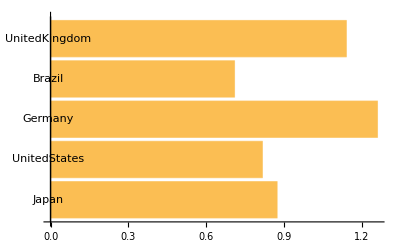

```mathematica
BarChart[result[[All,2]],ChartLabels->result[[All,1]],BarOrigin->Left]
```

```mathematica
(* 研究一组国家的手机使用量情况 *)
data = Cases[Table[{country,CountryData[country,"CellularPhones"]/CountryData[country,"Population"]},{country,CountryData["Asia"]}],{_,_Quantity}]
```

{{Afghanistan,0.202909 /person},{Armenia,1.03833 /person},{Azerbaijan,0.645812 /person},{Bahrain,0.84673 /person},{Bangladesh,0.271056 /person},{Bhutan,0.325293 /person},{Brunei,0.859462 /person},{Cambodia,0.253425 /person},{China,0.445508 /person},{Egypt,0.40331 /person},{Georgia,0.690641 /person},{Hong Kong,1.54464 /person},{India,0.251369 /person},{Indonesia,0.513953 /person},{Iran,0.511948 /person},{Iraq,0.435801 /person},{Israel,1.03772 /person},{Japan,0.87285 /person},{Jordan,0.520777 /person},{Kazakhstan,0.794099 /person},{Kuwait,0.680707 /person},{Kyrgyzstan,0.52022 /person},{Laos,0.277935 /person},{Lebanon,0.209071 /person},{Macau,1.43622 /person},{Malaysia,0.856238 /person},{Maldives,0.805908 /person},{Mongolia,0.537834 /person},{Myanmar,0.00675224 /person},{Nepal,0.144148 /person},{Oman,0.630426 /person},{Pakistan,0.398474 /person},{Philippines,0.621614 /person},{Qatar,0.584153 /person},{Russia,1.36721 /person},{Saudi Arabia,1.03407 /person},{Singapore,1.08977 /person},{South Korea,0.889559 /person},{Sri Lanka,0.517551 /person},{Syria,0.403194 /person},{Tajikistan,0.38516 /person},{Thailand,0.888252 /person},{Turkey,0.78047 /person},{Turkmenistan,0.188213 /person},{United Arab Emirates,0.946143 /person},{Uzbekistan,0.380461 /person},{Vietnam,0.719139 /person},{West Bank,0.422182 /person},{Yemen,0.124053 /person}}

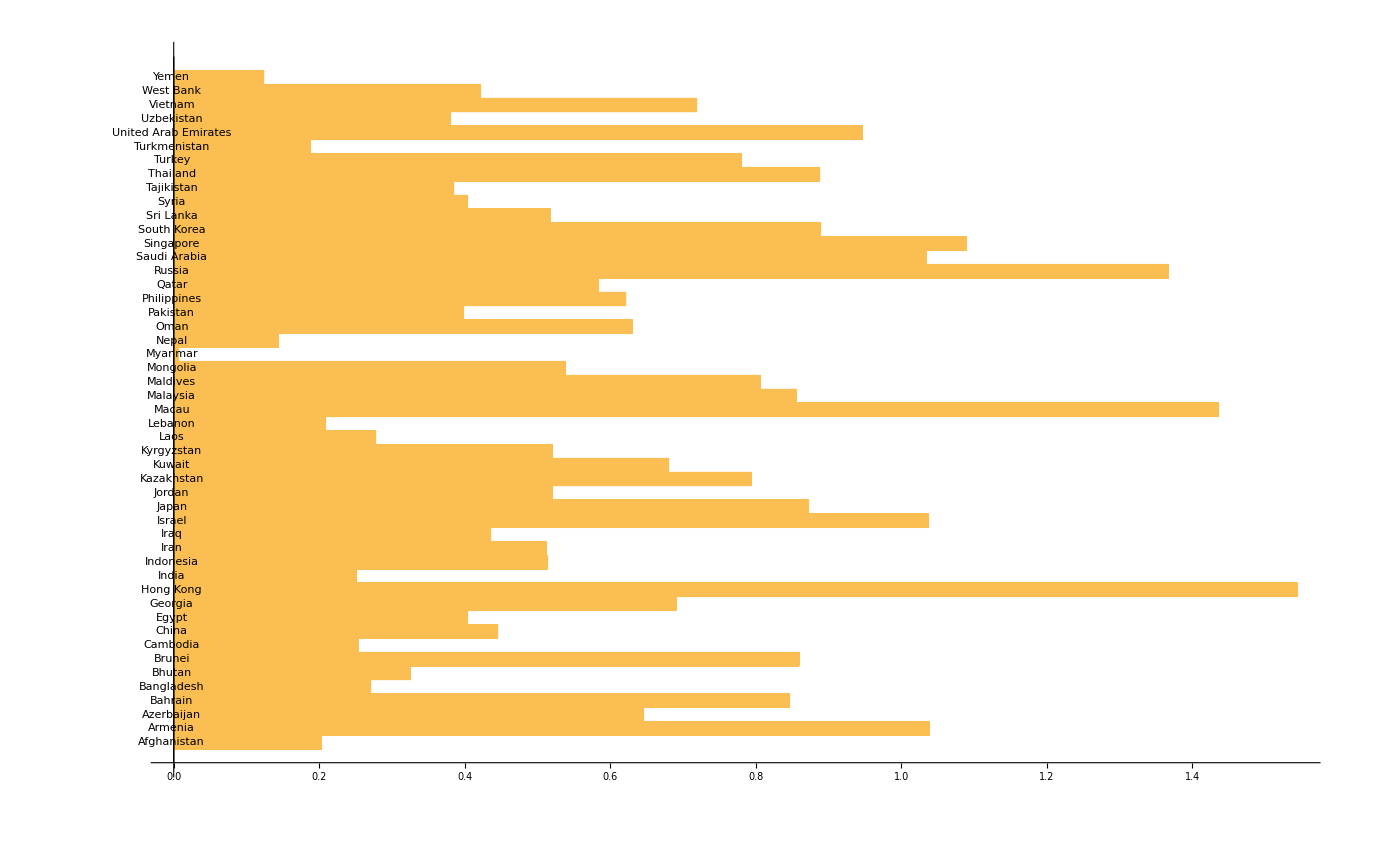

```mathematica
BarChart[data[[All,2]],ChartLabels->data[[All,1]],BarOrigin->Left]
```

```mathematica
(* 计算型金融数据 *)
```

{Fri 24 Feb 2023,146.71 $}

```mathematica
FinancialData["AAPL"] (* 查找某一家公司的股价 *)
```

146.71 $

```mathematica
(* 探索金融实体的可用属性 *)
Short[FinancialData["Properties"]]
```

{AdjustedClose,AdjustedHigh,AdjustedLow,AdjustedOHLC,AdjustedOHLCV,AdjustedOpen,AdjustedRange,Ask,«61»,SICCode,StandardName,Symbol,Volatility20Day,Volatility250Day,Volatility50Day,Volume,Website}

```mathematica
Length[FinancialData["Properties"]]
```

77

```mathematica
FinancialData["AAPL","LatestTrade"]
```

{Fri 24 Feb 2023,146.71 $}

```mathematica
(* 搜索苹果公司从2016年开始到目前的股价变化 *)
FinancialData["AAPL",{2016,1,1}]
```

TimeSeries[…]

```mathematica
FinancialData["AAPL",{{2010,12,15},{2022,2,2}}]
```

TimeSeries[…]

```mathematica
(* 可以使用DateListPlot函数对时间序列进行图形绘制 *)
```

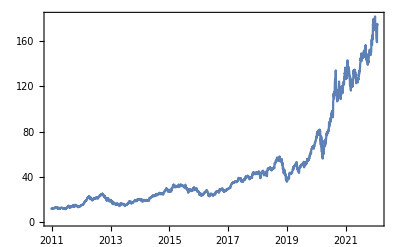

```mathematica
DateListPlot[FinancialData["AAPL",{{2010,12,15},{2022,2,2}}]]
```

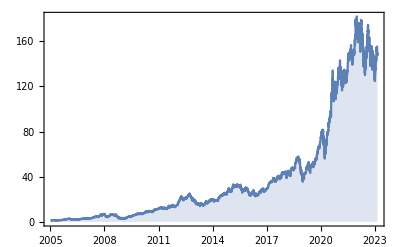

TimeSeries[…]

```mathematica
DateListPlot[FinancialData["AAPL",{2005,1}],Joined->True,Filling->Bottom]
```

```mathematica
FinancialData["AAPL",{{2010,1,1},{2010,1,31}}]
```

TimeSeries[…]

```mathematica
Normal[%]
```

{{Mon 4 Jan 2010 00:00:00GMT+8,7.64 $},{Tue 5 Jan 2010 00:00:00GMT+8,7.66 $},{Wed 6 Jan 2010 00:00:00GMT+8,7.53 $},{Thu 7 Jan 2010 00:00:00GMT+8,7.52 $},{Fri 8 Jan 2010 00:00:00GMT+8,7.57 $},{Mon 11 Jan 2010 00:00:00GMT+8,7.50 $},{Tue 12 Jan 2010 00:00:00GMT+8,7.42 $},{Wed 13 Jan 2010 00:00:00GMT+8,7.52 $},{Thu 14 Jan 2010 00:00:00GMT+8,7.48 $},{Fri 15 Jan 2010 00:00:00GMT+8,7.35 $},{Tue 19 Jan 2010 00:00:00GMT+8,7.68 $},{Wed 20 Jan 2010 00:00:00GMT+8,7.56 $},{Thu 21 Jan 2010 00:00:00GMT+8,7.43 $},{Fri 22 Jan 2010 00:00:00GMT+8,7.06 $},{Mon 25 Jan 2010 00:00:00GMT+8,7.25 $},{Tue 26 Jan 2010 00:00:00GMT+8,7.35 $},{Wed 27 Jan 2010 00:00:00GMT+8,7.42 $},{Thu 28 Jan 2010 00:00:00GMT+8,7.12 $},{Fri 29 Jan 2010 00:00:00GMT+8,6.86 $}}

```mathematica
%[[All,2]]
```

{7.64 $,7.66 $,7.53 $,7.52 $,7.57 $,7.50 $,7.42 $,7.52 $,7.48 $,7.35 $,7.68 $,7.56 $,7.43 $,7.06 $,7.25 $,7.35 $,7.42 $,7.12 $,6.86 $}

```mathematica
Mean[%]
```

7.42 $

```mathematica
(* 基于Table构造数据集，由苹果公司在2005年到2011年间的年份以及该年对应的平均收盘价组成 *)
closingPrice = Table[
		{year,Mean[Normal[FinancialData["AAPL",{{year,1,1},{year,12,31}}][[All,2]]]]},
		{year,2005,2011,1}
];
```

Part::partd: 部分指定 TemporalData[TimeSeries,{{{1.13,1.14,1.15,1.15,1.24,1.23,1.15,1.17,1.25,1.25,«242»}},{{{3313699200,3313785600,3313872000,3313958400,3314044800,3314304000,3314390400,3314476800,3314563200,3314649600,«242»}}},1,{Continuous,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,ResamplingMethod→{Interpolation,InterpolationOrder→1}}},True,12.]⟦All,2⟧ 比对象深度更长.

Part::partd: 部分指定 TemporalData[TimeSeries,{{{2.67,2.68,2.66,2.72,2.72,2.89,3.00,3.01,3.06,3.03,«241»}},{{{3345235200,3345321600,3345408000,3345494400,3345753600,3345840000,3345926400,3346012800,3346099200,3346444800,«241»}}},1,{Continuous,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,ResamplingMethod→{Interpolation,InterpolationOrder→1}}},True,12.]⟦All,2⟧ 比对象深度更长.

Part::partd: 部分指定 TemporalData[TimeSeries,{{{2.99,3.06,3.04,3.05,3.31,3.46,3.42,3.38,3.47,3.39,«241»}},{{{3376771200,3376857600,3376944000,3377203200,3377289600,3377376000,3377462400,3377548800,3377894400,3377980800,«241»}}},1,{Continuous,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,ResamplingMethod→{Interpolation,InterpolationOrder→1}}},True,12.]⟦All,2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

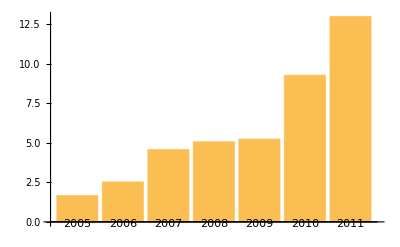

```mathematica
BarChart[closingPrice[[All,2]],BarOrigin->Bottom,ChartLabels->closingPrice[[All,1]]]
```

```mathematica
(* 数学数据 *)
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

```mathematica
KnotData["FigureEight"]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* 绘制Peterson图 *)
```

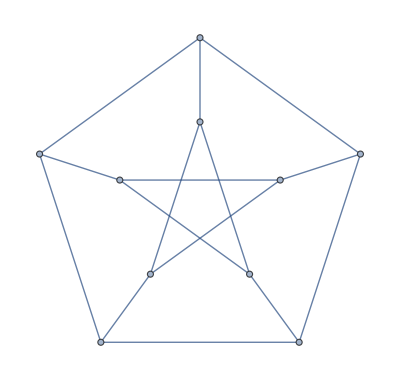

```mathematica
PetersenGraph[]
```

```mathematica
GraphData["PetersenGraph","Classes"](* 得到Peterson图的分类 *)
```

{AlmostHamiltonian,ArcTransitive,Biconnected,Biplanar,Bridgeless,Cage,ChromaticallyUnique,Class2,Connected,Cubic,Cyclic,DeterminedByResistance,DeterminedBySpectrum,DistanceRegular,DistanceTransitive,Doublecross,EdgeTransitive,GeneralizedPetersen,Geodetic,Graceful,Hypohamiltonian,IGraph,Imperfect,Integral,Kneser,Local,MaximallyNonhamiltonian,Moore,Noncayley,Nonempty,Noneulerian,Nonhamiltonian,Nonplanar,Odd,PerfectMatching,ProjectivePlanar,Regular,Simple,Snark,SquareFree,StronglyRegular,Symmetric,Toroidal,Traceable,TriangleFree,UnitDistance,VertexTransitive,WeakSnark}

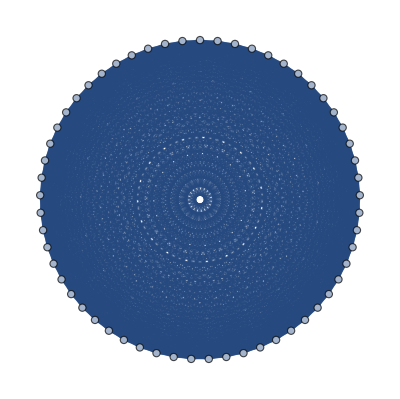

```mathematica
GraphData["PerkelGraph","ComplementGraph"] (* 获取比德森图的完全补图 *)
```

```mathematica
(* 地理数据 *)
CityData["London","Population"]
```

8673713 people

```mathematica
CityData[{"Paris", "IleDeFrance", "France"},"Population"]
```

2206488 people

```mathematica
CityData[{"Paris", "Illinois"},"Population"]
```

8291 people

8291 people

```mathematica
(* CityData中的有趣指令极其灵活的输入范式 *)
CityData[{"Chicago", "Illinois", "UnitedStates"},"Coordinates"]
```

{41.8376,-87.6818}

```mathematica
CityData[{"Chicago", "Illinois", "UnitedStates"},"Elevation"]
```

179 m

```mathematica
CityData[{"Boston", "Massachusetts", "UnitedStates"},"Elevation"]
```

14 m

```mathematica
(* 使用自由格式输入来比较两个城市海拔的高度 *)
```

{14. m,179. m}

```mathematica
UnitSimplify[{Quantity[45.9317585301837270341`2.,"Feet"],Quantity[587.2703412073490813648`3.,"Feet"]}]
```

{14. m,0.179 km}

```mathematica
(* 找出伊利诺伊州的大城市 *)
CityData[{Large,"Illinois","UnitedStates"}]
```

{Chicago,Aurora,Joliet,Naperville,Rockford,Elgin,Springfield,Peoria}

```mathematica
(* 科学和技术数据 *)
Short[ChemicalData[All]]
```

{liquid hydrogen,hydrogen,deuterium hydride,liquid helium,helium,tritium hydride,deuterium,tritium deuteride,hydrogen-t2,lithium,lithium hydride,lithium deuteride,beryllium,boron,beryllium hydride,diamond,activated charcoal,graphite,carbon-13,borane,liquid methane,methane,ammonia,methane-13 C,methane-d 1,steam,ice,water,ammonia-15 N,methane-d 2,methane-d 3,deuterium fluoride,hydrofluoric acid,hydrogen fluoride,water-18 O,heavy water,ammonia-d 3,methane-d 4,liquid neon,neon,ammonia-15 N,d 3,methane-13 C,d 4,lithium borohydride,methyllithium,water-t2,lithium amide,sodium,lithium hydroxide,sodium hydride,magnesium,boron nitride,lithium deuteroxide,beryllium oxide,lithium fluoride,acetylene,magnesium hydride,aluminum,hydrogen cyanide,diborane,borane-ammonia complex,carbon monoxide,carbon-13C monoxide,liquid nitrogen,nitrogen,acetylene-d 2,ethylene,silicon,dry air,liquid air,lithium oxide,nitrogen-15 N2,nitric oxide,formaldehyde,paraform,diazine,beryllium carbide,ethylene-13 C2,ethane,beryllium boride,black phosphorus,red phosphorus,nitric-15 noxide,formaldehyde-13 c,methylamine,ethane-13 C1,ethane-d 1,sulfur 32,liquid oxygen,oxygen,paraformaldehyde-d 2,formaldehyde-d 2,methanol,diazane,ethane-13 C2,mixed sulfur,ethylene-d 4,terminal dimethyl,silane,nitric-15 noxide-18 O,hydroxylamine,methanol-13 C,methanol-d,methan-d 1-ol,diborane-d 610%in D2,electronic grade,lithium-aluminum alloy,sulfur 34,phosphine,hydrogen peroxide,fluoromethane,methanol-18 O,methan-d 2-ol,«43867»,n-acetyl-alpha-D-glucosaminyl-(1->4)-beta-D-glucuronosyl-(1->4)-n-acetyl-alpha-D-glucosaminylproteoglycan,beta-D-glucuronosyl-(1->4)-n-acetyl-alpha-D-glucosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,beta-D-galactosyl-1,4-n-acetyl-beta-D-glucosaminylglycopeptide,n-acetyl-beta-D-glucosaminyl-glycopeptide,beta-D-glucuronosyl-(1->4)-n-acetyl-alpha-D-glucosaminylproteoglycan,4,5-dioxo-3α,4,5,6,7,8,9,9β-octahydro-1h pyrrolo[2,3-f]quinoline-2,7,9-tricarboxylate,1,4-beta-D-galactosyl-(alpha-1,3-L-fucosyl)-n-acetyl-D-glucosaminyl-r,1,4-beta-D-galactosyl-n-acetyl-D-glucosaminyl-r,beta-D-glucuronosyl-(1->3)-n-acetyl-beta-D-galactosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,ndp-aldose,n-palmitoylglycoprotein,calmodulin n6-methyl-L-lysine,glycoprotein,oligosaccharide containing 6-methyl-D-glucose units,o-palmitoylglycoprotein,mucus glycoprotein,oligoglycosylglucose,o-beta-D-xylosylprotein,[3-methylcrotonoyl-CoA:carbon-dioxide ligase(adp-forming)],colanic acid,mlps,propionyl-amp,alpha-n-acetyl-D-glucosaminyl-(1->4)-beta-D-glucuronosyl-(1->3)-beta-D-galactosyl-(1->3)-beta-D-galactosyl-(1->4)-beta-D-xylosylproteoglycan,oligoglycosylglucosylceramide,[acetyl-CoA carboxylase],a 4-hydroxyacid,histone-L-lysine,apo-[3-methylcrotonoyl-CoA:carbon-dioxide ligase (adp-forming)],[acetyl-CoA carboxylase] phosphate,1,4-alpha-D-glucooligosaccharide,heparosan-n-sulfate l-iduronate,n-acetyl-beta-D-galactosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,cutin monomer,n-acetyl-alpha-D-glucosaminyl-(1->4)-beta-D-glucuronosylproteoglycan,D-mannosylglycoprotein,excised base,n-acetyl-D-galactosaminoglycan,external aldimine,6-(d-glucose-1-phospho)-D-mannosylglycoprotein,alpha-D-aldose 1-phosphate,protein beta-D-galactosyl-L-hydroxylysine,caldesmon phosphate,caldesmon,myosin light-chain,myosin light-chain phosphate,cutin,D-galactosaminoglycan,calmodulin l-lysine,L-ala-D-glu-2pm,a phospholipid methylene fatty acid,c20 skeleton,methyl-beta-D-glucuronide,c19 skeleton,17a-hydroxy-progesterone,D-(-)-3-hydroxybutyrate,2-monoacylglycerol,1-monoacylglycerol,allo-4-hydroxy-D-proline,L-cysteine sulfinate,3-ketothreonine,an alpha amino acid ester,[formate c acetyltransferase]-glycine,[formate c acetyltransferase]-glycin -2-yl radical,protein c-terminal s-farnesyl-L-cysteine,protein c-terminal s-farnesyl-L-cysteine methyl ester,protein n6-methyl-L-lysine,protein-n-ubiquityl-lysine,protein tyrosine-o-sulfate,protein-n-acetyl-D-glucosaminyl)hydroxyproline,antidiuretic hormone,heparan sulfate,chromomycin a3,dextran,fumonisin b2,growth hormone-releasing hormone,hyaluronate,low density lipoprotein,signal recognition particle,trichostatin a,α-amanatin,ammonium metatungstate hexahydrate,cerium(III) acetate sesqihydrate,xenon fluoride undecafluoroantimonate,bacteriochlorophyll b,5-hydroxybenzimidazolylcobamide,co-5-hydroxybenzimidazolylcob(I)amide,ferric enterobactin,quinine sulfate dihydrate,methyl cellulose,sodium hexachloroiridate(IV) hexahydrate,brij58,brij78,triton®X-100 reduced,dihydrogen hexahydroxyplatinate(IV),carbonyldihydridotris(triphenylphosphine)ruthenium(II),dihydridotetrakis(triphenylphosphine)ruthenium(II),4-(2,3-dihydroxypropyl)-2-(2-methylene-4,4-dimethylpentyl)succinate potassium salt,triarylsulfonium hexafluoroantimonate salts,acetic acid,alkyl(C9 to C11)esters mixture,glycolic acid ethoxylate oleyl ether,cytosine-2,4-13 C2,15 N3,PSS-isooctyl substituted.cage mixture,n=8,10,12,3-acetylpyridine-nad,bacteriochlorophyll c,tetraearbonyldihydroiron,fe-mo cofactor,1,2-dehydroreticuline,sulfoquinovosyldiacylglycerol,iron phosphide (1:1),cobyrate,ag4}

```mathematica
Length[ChemicalData[All]]
```

44089

```mathematica
Length[ChemicalData["Properties"]]
```

100

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

-Graphics3D-

```mathematica
(* ElementData可用于查找关于元素和元素基团的信息 *)
ElementData["Gold","MolarVolume"]
```

10. cm^3/mol

```mathematica
ElementData["NobleGas"]
```

{helium,neon,argon,krypton,xenon,radon,oganesson}

```mathematica
(* 元素基团 *)
Short[ElementData["Groups"]]
```

{elements,group 1 elements,group 2 elements,group 3 elements,group 4 elements,group 5 elements,group 6 elements,group 7 elements,group 8 elements,group 9 elements,group 10 elements,group 11 elements,group 12 elements,group 13 elements,group 14 elements,group 15 elements,group 16 elements,group 17 elements,group 18 elements,period 1 elements,period 2 elements,period 3 elements,period 4 elements,period 5 elements,period 6 elements,period 7 elements,alkali metals,alkaline earth metals,transition metals,chalcogens,halogens,noble gases,lanthanides,actinides,solid elements,liquid elements,gaseous elements,s-block elements,p-block elements,d-block elements,f-block elements,conductors,semiconductors,insulators,ferromagnetic elements,paramagnetic elements,diamagnetic elements,antiferromagnetic elements,non-metallic elements,poor metals,metalloids,metallic elements,rare earth metals,noble metals,platinum metals,precious metals,coinage metals,naturally occurring elements,synthetic elements,stable elements,radioactive elements,very unstable elements,super-heavy elements,big bang elements,cosmic ray fission elements,merging neutron stars elements,exploding massive star elements,dying low mass star elements,exploding white dwarf elements,synthetic elements}

```mathematica
ProteinData["SERPINA3","MoleculePlot"]
```

-Graphics3D-

```mathematica
ProteinData["SERPINA3","BiologicalProcesses"]
```

{AcutePhaseResponse,InflammatoryResponse,RegulationOfLipidMetabolicProcess}

```mathematica
GenomeData["ZXDB","ProteinNames"]
```

{zinc finger, X-linked, duplicated B}

```mathematica
GenomeLookup["GATTACAGATTACAGATTA"]
```

{{{Chromosome2,1},{87696557,87696575}},{{Chromosome2,-1},{131142192,131142210}},{{Chromosome4,-1},{178364156,178364174}}}

```mathematica
(* 语言数据 *)
DictionaryLookup[{"English","e"~~___~~"u"}](* ~~<>~~表示使用通配符，<>中的内容为通配符的具体表达式 ___表示任意字符组合*)
```

{ecru,ecu,emu}

```mathematica
DictionaryLookup[{"French","e"~~___~~"u"}]
```

{eau,encouru,enjeu,entendu,entr'aperçu,entretenu,entrevu,escabeau,esquimau,essieu,eu,exclu,exigu}

```mathematica
(* 翻译 *)
WordTranslation["enjeu","French"->"English"]
```

{stake,wager}

```mathematica
WordTranslation["enjeu","French"->All]
```

<|English→{stake,wager},Spanish→{apuesta,estaca,interés,poste,apostar},Portuguese→{aposta,estaca,parte,participação,poste,apostar,arriscar},Japanese→{杙,杭,棒杙,棒杭,火刑,賭す,賭ける,賭する,利害関係},German→{Anteil,Bedeutung,Einsatz,Pfahl,Wette,wetten},Italian→{interesse,palo,picchetto,posta,quota,scommessa,scommettere},Dutch→{aandeel,belang,inzet,paal,staak,weddenschap,wedden,verwedden},Swedish→{andel,insats,intresse,påle,stake,stolpe,vad,slå vad},Latin→{palus,talea}|>

```mathematica
(* 语种识别 *)
LanguageIdentify["駆ける"]
```

Japanese

```mathematica
(* 使用精选专业数据进行关系可视化 *)
listOfAllCountries = CountryData[All];
```

```mathematica
results = Table[
	{i,CountryData[i,"CellularPhones"]/CountryData[i,"Population"]},{i,listOfAllCountries}
];
results[40;;50]
```

{{Afghanistan,0.202909 /person},{Aland Islands,Missing[NotAvailable] (1/29013 /person)},{Albania,1.09152 /person},{Algeria,0.726801 /person},{American Samoa,0.0407631 /person},{Andorra,0.830933 /person},{Angola,0.206088 /person},{Anguilla,Missing[NotAvailable] (1/15002 /person)},{Antigua and Barbuda,1.39482 /person},{Argentina,1.02905 /person},{Armenia,1.03833 /person},{Aruba,1.1315 /person},{Australia,0.867455 /person},{Austria,1.20092 /person},{Azerbaijan,0.645812 /person},{Bahamas,0.910494 /person},{Bahrain,0.84673 /person},{Bangladesh,0.271056 /person},{Barbados,1.41281 /person},{Belarus,0.860168 /person},{Belgium,1.02007 /person},{Belize,0.402474 /person},{Benin,0.283341 /person},{Bermuda,1.26861 /person},{Bhutan,0.325293 /person},{Bolivia,0.413774 /person},{Caribbean Netherlands,Missing[NotAvailable] (1/26221 /person)},{Bosnia and Herzegovina,0.968978 /person},{Botswana,0.631815 /person},{Bouvet Island,Missing[NotAvailable]/Missing[NoResidentPopulation]},{Brazil,0.708703 /person},{British Indian Ocean Territory,Missing[NotAvailable] (1/2500 /person)},{British Virgin Islands,Missing[NotAvailable] (1/30237 /person)},{Brunei,0.859462 /person},{Bulgaria,1.51116 /person},{Burkina Faso,0.122134 /person},{Burundi,0.0404165 /person},{Cambodia,0.253425 /person},{Cameroon,0.232085 /person},{Canada,0.585353 /person},{Cape Verde,0.499417 /person},{Cayman Islands,0.514303 /person},{Central African Republic,0.0318856 /person},{Chad,0.110131 /person},{Chile,0.774034 /person},{China,0.445508 /person},{Christmas Island,Missing[NotAvailable] (1/1513 /person)},{Cocos Keeling Islands,Missing[NotAvailable] (1/550 /person)},{Colombia,0.81294 /person},{Comoros,0.113188 /person},{Cook Islands,Missing[NotAvailable] (1/17564 /person)},{Costa Rica,0.370343 /person},{Croatia,1.43227 /person},{Cuba,0.0292882 /person},{Curacao,Missing[NotAvailable] (1/164100 /person)},{Cyprus,0.842117 /person},{Czech Republic,1.28679 /person},{Democratic Republic of the Congo,Missing[NotAvailable] (1/89561404 /person)},{Denmark,1.1847 /person},{Djibouti,0.114218 /person},{Dominica,1.38906 /person},{Dominican Republic,0.664689 /person},{East Timor,Missing[NotAvailable] (1/1318442 /person)},{Ecuador,0.6542 /person},{Egypt,0.40331 /person},{El Salvador,1.07161 /person},{Equatorial Guinea,0.246617 /person},{Eritrea,0.0306311 /person},{Estonia,1.90305 /person},{Ethiopia,0.0170013 /person},{Falkland Islands,Missing[NotAvailable] (1/3483 /person)},{Faroe Islands,Missing[NotAvailable] (1/48865 /person)},{Fiji,0.669311 /person},{Finland,1.23269 /person},{France,0.88814 /person},{French Guiana,Missing[NotAvailable] (1/298682 /person)},{French Polynesia,Missing[NotAvailable] (1/280904 /person)},{French Southern And Antarctic lands,Missing[NotAvailable] (1/196 /person)},{Gabon,0.584079 /person},{Gambia,0.48254 /person},{Gaza Strip,Missing[NotAvailable] (1/1763387 /person)},{Georgia,0.690641 /person},{Germany,1.25947 /person},{Ghana,0.372363 /person},{Gibraltar,Missing[NotAvailable] (1/33691 /person)},{Greece,1.32392 /person},{Greenland,0.983161 /person},{Grenada,0.533439 /person},{Guadeloupe,Missing[NotAvailable] (1/400127 /person)},{Guam,0.580627 /person},{Guatemala,0.834394 /person},{Guernsey,Missing[NotAvailable] (1/65605 /person)},{Guinea,0.292428 /person},{Guinea-Bissau,0.254145 /person},{Guyana,0.35772 /person},{Haiti,0.280639 /person},{Honduras,0.627053 /person},{Hong Kong,1.54464 /person},{Hungary,1.2654 /person},{Iceland,1.00428 /person},{India,0.251369 /person},{Indonesia,0.513953 /person},{Iran,0.511948 /person},{Iraq,0.435801 /person},{Ireland,1.0849 /person},{Isle of Man,Missing[NotAvailable] (1/85032 /person)},{Israel,1.03772 /person},{Italy,1.49418 /person},{Ivory Coast,0.396123 /person},{Jamaica,0.919681 /person},{Japan,0.87285 /person},{Jersey,Missing[NotAvailable] (1/95732 /person)},{Jordan,0.520777 /person},{Kazakhstan,0.794099 /person},{Kenya,0.303202 /person},{Kiribati,0.00837198 /person},{Kosovo,Missing[NotAvailable] (1/1859203 /person)},{Kuwait,0.680707 /person},{Kyrgyzstan,0.52022 /person},{Laos,0.277935 /person},{Latvia,1.18439 /person},{Lebanon,0.209071 /person},{Lesotho,0.27121 /person},{Liberia,0.14473 /person},{Libya,0.702634 /person},{Liechtenstein,0.891523 /person},{Lithuania,1.845 /person},{Luxembourg,1.12944 /person},{Macau,1.43622 /person},{North Macedonia,1.2009 /person},{Madagascar,0.174614 /person},{Malawi,0.0931001 /person},{Malaysia,0.856238 /person},{Maldives,0.805908 /person},{Mali,0.16982 /person},{Malta,0.873391 /person},{Marshall Islands,0.0168936 /person},{Martinique,Missing[NotAvailable] (1/375265 /person)},{Mauritania,0.449924 /person},{Mauritius,0.812459 /person},{Mayotte,0.176311 /person},{Mexico,0.584067 /person},{Micronesia,0.295598 /person},{Moldova,0.600753 /person},{Monaco,Missing[NotAvailable] (1/39244 /person)},{Mongolia,0.537834 /person},{Montenegro,1.17027 /person},{Montserrat,Missing[NotAvailable] (1/4999 /person)},{Morocco,0.618135 /person},{Mozambique,0.140936 /person},{Myanmar,0.00675224 /person},{Namibia,0.414024 /person},{Nauru,Missing[NotAvailable] (1/10834 /person)},{Nepal,0.144148 /person},{Netherlands,1.2038 /person},{New Caledonia,0.688197 /person},{New Zealand,0.958062 /person},{Nicaragua,0.469164 /person},{Niger,0.0783929 /person},{Nigeria,0.305562 /person},{Niue,Missing[NotAvailable] (1/1618 /person)},{Norfolk Island,Missing[NotAvailable] (1/2196 /person)},{Northern Mariana Islands,0.355717 /person},{North Korea,Missing[NotAvailable] (1/25778815 /person)},{Norway,0.968577 /person},{Oman,0.630426 /person},{Pakistan,0.398474 /person},{Palau,0.674773 /person},{Panama,0.907406 /person},{Papua New Guinea,0.0670614 /person},{Paraguay,0.834821 /person},{Peru,0.635446 /person},{Philippines,0.621614 /person},{Pitcairn Islands,Missing[NotAvailable] (1/56 /person)},{Poland,1.16064 /person},{Portugal,1.4622 /person},{Puerto Rico,1.17231 /person},{Qatar,0.584153 /person},{Republic of the Congo,0.327468 /person},{Réunion,Missing[NotAvailable] (1/895308 /person)},{Romania,1.27183 /person},{Russia,1.36721 /person},{Rwanda,0.102117 /person},{Saint Barthelemy,Missing[NotAvailable] (1/9885 /person)},{Saint Helena, Ascension and Tristan da Cunha,Missing[NotAvailable] (1/6071 /person)},{Saint Kitts and Nevis,1.50399 /person},{Saint Lucia,0.923601 /person},{Saint Martin,Missing[NotAvailable] (1/38659 /person)},{Saint Pierre and Miquelon,Missing[NotAvailable] (1/5795 /person)},{Saint Vincent and the Grenadines,1.17261 /person},{Samoa,0.624968 /person},{San Marino,0.707172 /person},{São Tomé and Príncipe,0.22358 /person},{Saudi Arabia,1.03407 /person},{Senegal,0.321856 /person},{Serbia,1.09421 /person},{Seychelles,0.950539 /person},{Sierra Leone,0.126464 /person},{Singapore,1.08977 /person},{Sint Maarten,Missing[NotAvailable] (1/42882 /person)},{Slovakia,1.01106 /person},{Slovenia,0.98844 /person},{Solomon Islands,0.0436759 /person},{Somalia,0.0394508 /person},{South Africa,0.758742 /person},{South Georgia and the South Sandwich Islands,Missing[NotAvailable] (1/30 /person)},{South Korea,0.889559 /person},{South Sudan,Missing[NotAvailable] (1/11193729 /person)},{Spain,1.06251 /person},{Sri Lanka,0.517551 /person},{Sudan,0.27347 /person},{Suriname,0.70913 /person},{Svalbard,Missing[NotAvailable] (1/2637 /person)},{Eswatini,0.458248 /person},{Sweden,1.07849 /person},{Switzerland,1.02797 /person},{Syria,0.403194 /person},{Taiwan,Missing[NotAvailable] (1/23816775 /person)},{Tajikistan,0.38516 /person},{Tanzania,0.217744 /person},{Thailand,0.888252 /person},{Togo,0.187171 /person},{Tokelau,Missing[NotAvailable] (1/1350 /person)},{Tonga,0.477516 /person},{Trinidad and Tobago,1.07539 /person},{Tunisia,0.727849 /person},{Turkey,0.78047 /person},{Turkmenistan,0.188213 /person},{Turks and Caicos Islands,Missing[NotAvailable] (1/38718 /person)},{Tuvalu,Missing[NotAvailable] (1/11792 /person)},{Uganda,0.187028 /person},{Ukraine,1.27349 /person},{United Arab Emirates,0.946143 /person},{United Kingdom,1.13957 /person},{United States,0.816113 /person},{United States Minor Outlying Islands,Missing[NotAvailable] (1/300 /person)},{United States Virgin Islands,0.768988 /person},{Uruguay,1.00981 /person},{Uzbekistan,0.380461 /person},{Vanuatu,0.117207 /person},{Vatican City,Missing[NotAvailable] (1/809 /person)},{Venezuela,0.952451 /person},{Vietnam,0.719139 /person},{Wallis and Futuna Islands,Missing[NotAvailable] (1/11246 /person)},{West Bank,0.422182 /person},{Western Sahara,Missing[NotAvailable] (1/597330 /person)},{Yemen,0.124053 /person},{Zambia,0.192505 /person},{Zimbabwe,0.111332 /person}}[40;;50]

```mathematica
results = Cases[Table[
	{i,CountryData[i,"CellularPhones"]/CountryData[i,"Population"]},{i,listOfAllCountries}
],{_,_Quantity}];
results[40;;50]
```

{{Afghanistan,0.202909 /person},{Albania,1.09152 /person},{Algeria,0.726801 /person},{American Samoa,0.0407631 /person},{Andorra,0.830933 /person},{Angola,0.206088 /person},{Antigua and Barbuda,1.39482 /person},{Argentina,1.02905 /person},{Armenia,1.03833 /person},{Aruba,1.1315 /person},{Australia,0.867455 /person},{Austria,1.20092 /person},{Azerbaijan,0.645812 /person},{Bahamas,0.910494 /person},{Bahrain,0.84673 /person},{Bangladesh,0.271056 /person},{Barbados,1.41281 /person},{Belarus,0.860168 /person},{Belgium,1.02007 /person},{Belize,0.402474 /person},{Benin,0.283341 /person},{Bermuda,1.26861 /person},{Bhutan,0.325293 /person},{Bolivia,0.413774 /person},{Bosnia and Herzegovina,0.968978 /person},{Botswana,0.631815 /person},{Brazil,0.708703 /person},{Brunei,0.859462 /person},{Bulgaria,1.51116 /person},{Burkina Faso,0.122134 /person},{Burundi,0.0404165 /person},{Cambodia,0.253425 /person},{Cameroon,0.232085 /person},{Canada,0.585353 /person},{Cape Verde,0.499417 /person},{Cayman Islands,0.514303 /person},{Central African Republic,0.0318856 /person},{Chad,0.110131 /person},{Chile,0.774034 /person},{China,0.445508 /person},{Colombia,0.81294 /person},{Comoros,0.113188 /person},{Costa Rica,0.370343 /person},{Croatia,1.43227 /person},{Cuba,0.0292882 /person},{Cyprus,0.842117 /person},{Czech Republic,1.28679 /person},{Denmark,1.1847 /person},{Djibouti,0.114218 /person},{Dominica,1.38906 /person},{Dominican Republic,0.664689 /person},{Ecuador,0.6542 /person},{Egypt,0.40331 /person},{El Salvador,1.07161 /person},{Equatorial Guinea,0.246617 /person},{Eritrea,0.0306311 /person},{Estonia,1.90305 /person},{Ethiopia,0.0170013 /person},{Fiji,0.669311 /person},{Finland,1.23269 /person},{France,0.88814 /person},{Gabon,0.584079 /person},{Gambia,0.48254 /person},{Georgia,0.690641 /person},{Germany,1.25947 /person},{Ghana,0.372363 /person},{Greece,1.32392 /person},{Greenland,0.983161 /person},{Grenada,0.533439 /person},{Guam,0.580627 /person},{Guatemala,0.834394 /person},{Guinea,0.292428 /person},{Guinea-Bissau,0.254145 /person},{Guyana,0.35772 /person},{Haiti,0.280639 /person},{Honduras,0.627053 /person},{Hong Kong,1.54464 /person},{Hungary,1.2654 /person},{Iceland,1.00428 /person},{India,0.251369 /person},{Indonesia,0.513953 /person},{Iran,0.511948 /person},{Iraq,0.435801 /person},{Ireland,1.0849 /person},{Israel,1.03772 /person},{Italy,1.49418 /person},{Ivory Coast,0.396123 /person},{Jamaica,0.919681 /person},{Japan,0.87285 /person},{Jordan,0.520777 /person},{Kazakhstan,0.794099 /person},{Kenya,0.303202 /person},{Kiribati,0.00837198 /person},{Kuwait,0.680707 /person},{Kyrgyzstan,0.52022 /person},{Laos,0.277935 /person},{Latvia,1.18439 /person},{Lebanon,0.209071 /person},{Lesotho,0.27121 /person},{Liberia,0.14473 /person},{Libya,0.702634 /person},{Liechtenstein,0.891523 /person},{Lithuania,1.845 /person},{Luxembourg,1.12944 /person},{Macau,1.43622 /person},{North Macedonia,1.2009 /person},{Madagascar,0.174614 /person},{Malawi,0.0931001 /person},{Malaysia,0.856238 /person},{Maldives,0.805908 /person},{Mali,0.16982 /person},{Malta,0.873391 /person},{Marshall Islands,0.0168936 /person},{Mauritania,0.449924 /person},{Mauritius,0.812459 /person},{Mayotte,0.176311 /person},{Mexico,0.584067 /person},{Micronesia,0.295598 /person},{Moldova,0.600753 /person},{Mongolia,0.537834 /person},{Montenegro,1.17027 /person},{Morocco,0.618135 /person},{Mozambique,0.140936 /person},{Myanmar,0.00675224 /person},{Namibia,0.414024 /person},{Nepal,0.144148 /person},{Netherlands,1.2038 /person},{New Caledonia,0.688197 /person},{New Zealand,0.958062 /person},{Nicaragua,0.469164 /person},{Niger,0.0783929 /person},{Nigeria,0.305562 /person},{Northern Mariana Islands,0.355717 /person},{Norway,0.968577 /person},{Oman,0.630426 /person},{Pakistan,0.398474 /person},{Palau,0.674773 /person},{Panama,0.907406 /person},{Papua New Guinea,0.0670614 /person},{Paraguay,0.834821 /person},{Peru,0.635446 /person},{Philippines,0.621614 /person},{Poland,1.16064 /person},{Portugal,1.4622 /person},{Puerto Rico,1.17231 /person},{Qatar,0.584153 /person},{Republic of the Congo,0.327468 /person},{Romania,1.27183 /person},{Russia,1.36721 /person},{Rwanda,0.102117 /person},{Saint Kitts and Nevis,1.50399 /person},{Saint Lucia,0.923601 /person},{Saint Vincent and the Grenadines,1.17261 /person},{Samoa,0.624968 /person},{San Marino,0.707172 /person},{São Tomé and Príncipe,0.22358 /person},{Saudi Arabia,1.03407 /person},{Senegal,0.321856 /person},{Serbia,1.09421 /person},{Seychelles,0.950539 /person},{Sierra Leone,0.126464 /person},{Singapore,1.08977 /person},{Slovakia,1.01106 /person},{Slovenia,0.98844 /person},{Solomon Islands,0.0436759 /person},{Somalia,0.0394508 /person},{South Africa,0.758742 /person},{South Korea,0.889559 /person},{Spain,1.06251 /person},{Sri Lanka,0.517551 /person},{Sudan,0.27347 /person},{Suriname,0.70913 /person},{Eswatini,0.458248 /person},{Sweden,1.07849 /person},{Switzerland,1.02797 /person},{Syria,0.403194 /person},{Tajikistan,0.38516 /person},{Tanzania,0.217744 /person},{Thailand,0.888252 /person},{Togo,0.187171 /person},{Tonga,0.477516 /person},{Trinidad and Tobago,1.07539 /person},{Tunisia,0.727849 /person},{Turkey,0.78047 /person},{Turkmenistan,0.188213 /person},{Uganda,0.187028 /person},{Ukraine,1.27349 /person},{United Arab Emirates,0.946143 /person},{United Kingdom,1.13957 /person},{United States,0.816113 /person},{United States Virgin Islands,0.768988 /person},{Uruguay,1.00981 /person},{Uzbekistan,0.380461 /person},{Vanuatu,0.117207 /person},{Venezuela,0.952451 /person},{Vietnam,0.719139 /person},{West Bank,0.422182 /person},{Yemen,0.124053 /person},{Zambia,0.192505 /person},{Zimbabwe,0.111332 /person}}[40;;50]

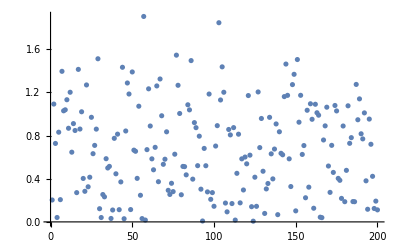

```mathematica
(* 对上述数据进行图形的绘制 *)
ListPlot[results[[All,2]]]
```

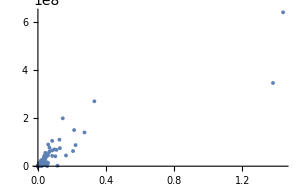

```mathematica
PopvsPhones = Table[{CountryData[i,"Population"],CountryData[i,"CellularPhones"]},{i,listOfAllCountries}];
ListPlot[PopvsPhones,PlotRange->All,ImageSize->300]
```

```mathematica
PopvsPhones = Table[Tooltip[{CountryData[i,"Population"],CountryData[i,"CellularPhones"]}],{i,listOfAllCountries}];(* 在内部每一个数据点加上提示条用于表示当前点的默认信息 *)
ListPlot[PopvsPhones,PlotRange->All,ImageSize->300]
```

-Graphics-

```mathematica
filter[x_]:=QuantityMagnitude[CountryData[x,"Population"]] > 2*10^7;
listOfCountries = Select[CountryData[All],filter];
listOfCountries
```

{Afghanistan,Algeria,Angola,Argentina,Australia,Bangladesh,Brazil,Burkina Faso,Cameroon,Canada,China,Colombia,Democratic Republic of the Congo,Egypt,Ethiopia,France,Germany,Ghana,India,Indonesia,Iran,Iraq,Italy,Ivory Coast,Japan,Kenya,Madagascar,Malaysia,Mali,Mexico,Morocco,Mozambique,Myanmar,Nepal,Niger,Nigeria,North Korea,Pakistan,Peru,Philippines,Poland,Russia,Saudi Arabia,South Africa,South Korea,Spain,Sri Lanka,Sudan,Taiwan,Tanzania,Thailand,Turkey,Uganda,Ukraine,United Kingdom,United States,Uzbekistan,Venezuela,Vietnam,Yemen}

```mathematica
result = Table[Tooltip[{CountryData[i,"Population"],CountryData[i,"CellularPhones"]},i],{i,listOfCountries}];(* 在内部每一个数据点加上提示条用于表示当前点的默认信息 *)
```

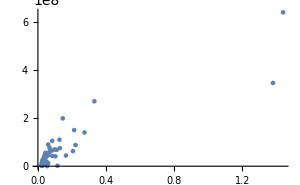

```mathematica
ListPlot[result,PlotRange->All,ImageSize->300]
```

```mathematica
filter[x_]:=10^12>QuantityMagnitude[CountryData[x,"GDP"]] > 10^11;
listOfCountries = Select[CountryData[All],filter];
listOfCountries
```

{Algeria,Argentina,Austria,Bangladesh,Belgium,Chile,Colombia,Cuba,Czech Republic,Denmark,Egypt,Ethiopia,Finland,Greece,Hong Kong,Hungary,Iran,Iraq,Ireland,Israel,Kazakhstan,Kuwait,Malaysia,Morocco,Netherlands,New Zealand,Nigeria,Norway,Pakistan,Peru,Philippines,Poland,Portugal,Puerto Rico,Qatar,Romania,Saudi Arabia,Singapore,Slovakia,South Africa,Sweden,Switzerland,Taiwan,Thailand,Turkey,Ukraine,United Arab Emirates,Venezuela,Vietnam}

```mathematica
PopvsPhones = Table[Tooltip[{CountryData[i,"Population"],CountryData[i,"CellularPhones"]}],{i,listOfCountries}];(* 在内部每一个数据点加上提示条用于表示当前点的默认信息 *)
```

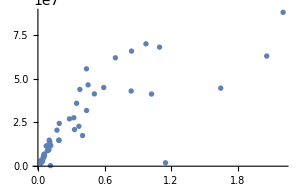

```mathematica
ListPlot[PopvsPhones,PlotRange->All,ImageSize->300]
```

```mathematica
(* 创建精选专业的数据表格 *)
TraditionalForm[{
	{1,2,3},
	{4,5,6},
	{7,8,9}
}]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
TraditionalForm[
	{
            {{1,2,3},
	{4,5,6}}		
      ,
	  {{7,8,9},{10,11,12}}
       ,
	 {{13,14,15},{16,17,18}}}
]
```

({1,2,3} | {4,5,6}
{7,8,9} | {10,11,12}
{13,14,15} | {16,17,18})

```mathematica
MatrixForm[%]
```

((1
2
3) | (4
5
6)
(7
8
9) | (10
11
12)
(13
14
15) | (16
17
18))

```mathematica
Row[{"item1","item2","item3"}]
```

item1item2item3

```mathematica
Row[{"item1",Spacer[20],"item2",Spacer[60],"item3"}]
```

item1item2item3

```mathematica
(* 设定元素之间固定的间隔 *)
Row[{"item1","item2","item3"},Spacer[15]]
```

item1item2item3

```mathematica
(* Column指令和Row指令类似 *)
Column[{"item1","item2","item3"},Spacer[30],Spacings->1](*Spacer是一行之内每一个元素时间的间距，Spacings表示行间距 *)
```

item1
item2
item3

```mathematica
(* Grid的使用方法 *)
```

```mathematica
Grid[
	{
  {"item1","item2"},
   {"item3","item4"}		
}
]
```

item1 | item2
item3 | item4

```mathematica
Grid[
	{
  {"item1","item2"},
   {"item3","item4"}		
},Frame->All
]
```

item1 | item2
item3 | item4

```mathematica
(* 专门用于排列文稿的函数TextGrid *)
TextGrid[
{
{"item1","item2"},
{"item3","item4"}
},Frame->All
]
```

item1 | item2
item3 | item4

```mathematica
(* TraditionForm封装Grid以更美观的显示表格 *)
f[x_]:=x^2;
values = Table[{i,f[i]},{i,1,10,1} ];
PrependTo[values,{"x","x^2"}]
```

{{x,x^2},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
TraditionalForm[%]
```

(x | x^2
1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100)

```mathematica
values
```

{{x,x^2},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
TraditionalForm[Grid[values,Frame->All]]
```

x | x^2
1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100

```mathematica
Row[{"Molecular weight:",Spacer[10],ChemicalData["Caffeine","MolecularMass"]}]
```

Molecular weight:194.2 u

```mathematica
TraditionalForm[Column[{
	ChemicalData["Caffeine","Name"],
	Row[{"Molecular weight:",Spacer[10],ChemicalData["Caffeine","MolecularWeight"],Spacer[5],ChemicalData["Caffeine","MolecularWeight","Units"]}],
	Row[{"Boiling Point:",Spacer[10],ChemicalData["Caffeine","BoilingPoint"],Spacer[5],ChemicalData["Caffeine","BoilingPoint","Uni"]}],
	ChemicalData["Caffeine","MoleculePlot"]
},Frame->All]]
```

ChemicalData::notsubprop: "Uni" 不是 ChemicalData 的一个已知子属性. 请使用子属性 " Properties " 以获取子属性列表.

caffeine
Molecular weight:194.2 uAtomicMassUnits
Boiling Point:—ChemicalData[Caffeine,BoilingPoint,Uni]
-Graphics3D-

```mathematica
Manipulate[
 TraditionalForm[
Column[{
 ChemicalData[chemical,"Name"],
Row[{"Molecular weight:",Spacer[10],ChemicalData[chemical,"MolecularWeight"],Spacer[5],ChemicalData[chemical,"MolecularWeight","Units"]}],
Row[{"Boiling Point:",Spacer[10],ChemicalData[chemical,"BoilingPoint"],Spacer[5],ChemicalData[chemical,"BoilingPoint","Units"]}],
ChemicalData[chemical,"MoleculePlot"]
},Frame->All]
],{chemical,{"Caffeine","Water","Acetone","Sucrose"}}
]
```

```mathematica
Clear[result,data,closingPrice,listOfAllCountries,PopvsPhones,filter,f,values]
```